## Sistema Hamiltoniano

```mathematica
J=({{0, 1}, {-1, 0}});
```

```mathematica
d[x_,y_]:={x^2-2x y,y^2-2x y};
H[x_,y_]:=Integrate[d[x,y][[1]],y]+c[x]
H[x,y]
```

x (x y-y^2)+c[x]

```mathematica
sol=DSolve[d[x,y][[2]]==-D[H[x,y], x],c[x],x]//First
```

{c[x]→C[1]}

```mathematica
H[x_,y_]:=H[x,y]/.sol//Evaluate
H[x,y]
```

x (x y-y^2)+C[1]

```mathematica
J . D[H[x,y],{{x,y}}]==d[x,y]//Expand
```

True

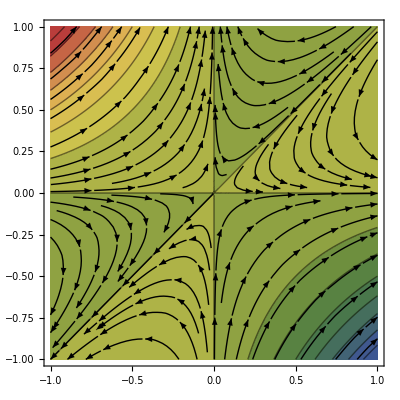

```mathematica
Show[
ContourPlot[H[x,y]/.C[1]-> 0,{x,-1,1},{y,-1,1},PlotRange->Full,ColorFunction->(ColorData["DarkRainbow"][#]&),MaxRecursion->7,Contours->15],
StreamPlot[J . D[H[x,y],{{x,y}}]//Evaluate,{x,-1,1},{y,-1,1},StreamStyle->Black,StreamScale->0.12,StreamPoints->50],
ImageSize-> 400
]
```

## Campo gradiente no toro

```mathematica
(*mapa do toro*)
Γ2[t_,u_]:={Cos[2Pi t] (2+Cos[2Pi u]),Sin[2Pi t] (2+Cos[2Pi u]),Sin[2Pi u]};
S2[t_,u_]:={Cos[2Pi t]Sin[Pi u],Sin[2Pi t] Sin[Pi u],Cos[Pi u]};
```

```mathematica
f[x_,y_]:=Cos[2Pi x]+Cos[2Pi y]
```

```mathematica
g[x_,y_]:=-Grad[f[x,y],{x,y}]//Evaluate
g[x,y]
```

{2 π Sin[2 π x],2 π Sin[2 π y]}

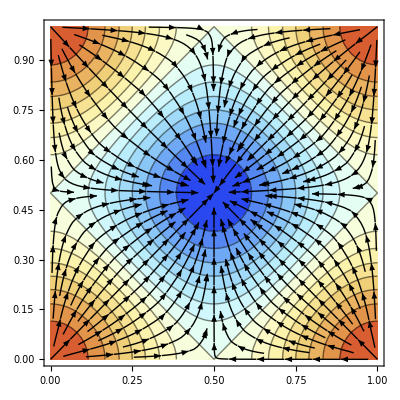

```mathematica
Show[
ContourPlot[f[x,y],{x,0,1},{y,0,1},PlotRange->Full,ColorFunction->(ColorData["LightTemperatureMap"][#]&),Contours->15],
StreamPlot[g[x,y],{x,0,1},{y,0,1},StreamStyle->Black],
ImageSize-> 400]
```

```mathematica
sp=StreamPlot[g[x,y],{x,0,1},{y,0,1},StreamStyle->Black,StreamPoints->Fine];
flux=Graphics3D[sp[[1]]/.Arrow[z_]:>Arrow[z/.{t_Real,u_Real}:>Γ2[t,u]],Boxed->False,Axes->False];
torus=ParametricPlot3D[Γ2[t,u],{t,0,1},{u,0,1},PlotTheme->"Classic",PlotStyle->Opacity[0.85],Mesh->None,Boxed->False,Axes->False];
Show[torus,flux,ImageSize->Large]
```

-Graphics3D-